# BSet 3: The Power of LTI

### Problem 1

#### Calculate the impulse response of a system that calculates the three element trailing average of the input: y[n]=1/3(x[n]+x[n-1]+x[n-2]) In other words, what does the output of the system look like if the input is x[n] = δ[n] – i.e., a x = 1 at n = 0 and 0 everywhere else?

```mathematica
h[n]=1/3(d[n]+x[n-1]+x[n-2])
```

```mathematica
δ[n_]:=0;
δ[0]:=1;

h[n_]:=1/3 δ[n]+1/3 δ[n-1]+1/3 δ[n-2];
```

```mathematica
Table[h[n],{n,0,5}]
```

{1/3,1/3,1/3,0,0,0}

### Problem 2: Given the x signal below, apply the filter to the signal

```mathematica
x={1,2,-3,0,0};
```

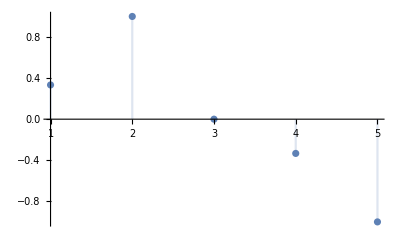

```mathematica
trailing={1/3,1/3,1/3};
processedBad=Join[x[[1]]*trailing,{0,0}]+Join[{0},x[[2]]*trailing,{0}]+Join[{0,0},x[[3]]*trailing];
DiscretePlot[processedBad[[n]],{n,1,5}]
```

## Impulse responses and convolution

### Problem 3

#### (a) Sketch output y[n]

```mathematica
ethernetX={1,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,1};
ethernetResponse={0.1,-0.08,0.06,-0.05,0.04,0.0};
```

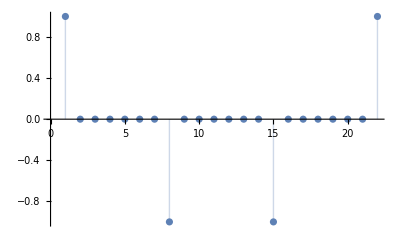

```mathematica
ListPlot[ethernetX,Filling->Axis]
```

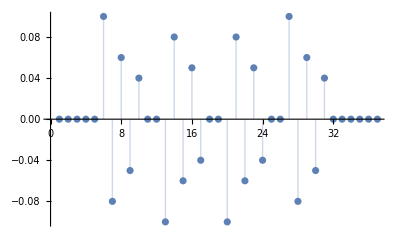

```mathematica
ListPlot[ListConvolve[
ethernetResponse,
Join[
ConstantArray[0,10],
ethernetX,
ConstantArray[0,10]
]
],Filling->Axis]
```

#### (b) What potential problems can you anticipate if the time between the ± 1 samples is too short?

It looks like the bits will interfere with each other

### 4. Slash playing guitar in a stairwell

#### (a) Explain why the recording of a finger being snapped is a decent approximation to the impulse response of this system

A finger being snapped is a very sharp, loud noise, and the response of the echos of the stairwell will be the response to the short snap sound.

#### (b) Using what you know about the convolution and impulse responses simulate the effect of the guitar sample being played in a stairwell.

```mathematica
SetDirectory[NotebookDirectory[]];
{fs,hStairwell,x}=Import["BSet3Files/guitar_stairwell.mat"];
fs=fs[[1,1]];
x=Flatten[x];
hStairwell=Flatten[hStairwell];
```

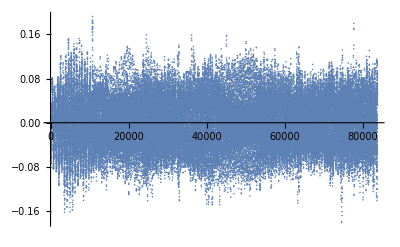

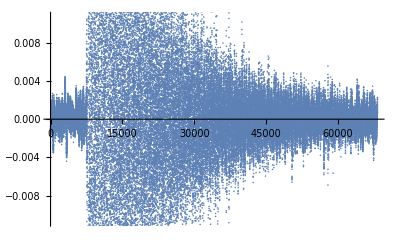

```mathematica
ListPlot[x]
ListPlot[hStairwell]
```

```mathematica
ListPlay[x,SampleRate->fs]
```

-Graphics-

```mathematica
guitarInStairwell=ListConvolve[hStairwell,x,1];
```

```mathematica
ListPlay[guitarInStairwell,SampleRate->fs]
```

-Graphics-

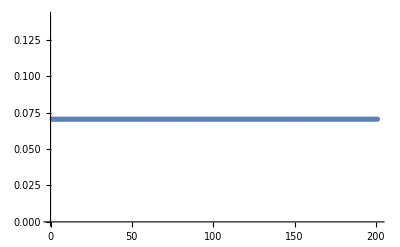

```mathematica
(* This is really cool and it's because of sinc *)
ListPlot[Abs[Fourier[Join[
ConstantArray[0,100],
{1},
ConstantArray[0,100]
]]]]
```

```mathematica
sincOrSomething=Integrate[Exp[I*ω*t],ω]
```

-(ⅈ ⅇ^(ⅈ t ω))/t

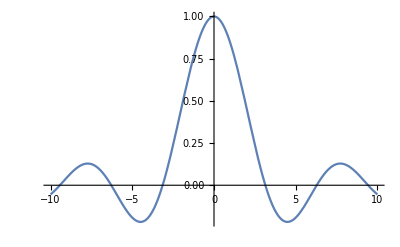

```mathematica
Plot[Re[sincOrSomething/.{ω->1}],{t,-10,10}]
```

### 5.

```mathematica
Subscript[Ω, c]=Pi/4;

q5$lowPass=Sin[Subscript[Ω, c]*n]/(n*π);
q5$lowPass//TraditionalForm
```

(sin((π n)/4))/(π n)

```mathematica
SetDirectory[NotebookDirectory[]];
q5$handel=Import["BSet2Files/handel.wav"];
```

#### (a)

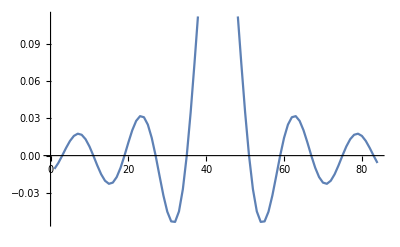

```mathematica
q5$n=Range[-42,41];
q5$h=Subscript[Ω, c]/Pi*Sinc[(Subscript[Ω, c]*n/Pi)*(Pi/2)]/.n->q5$n;
ListLinePlot[q5$h]
```

```mathematica
q5$x=q5$handel//AudioData;
q5$y=ListConvolve[q5$h,q5$x,1];
q5a$lowPassed=ListPlay[q5$y,SampleRate->QuantityMagnitude[AudioSampleRate[q5$handel]]]
```

-Graphics-

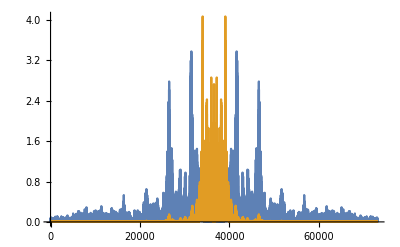

```mathematica
fftShift[x_]:=RotateRight[Fourier[x],Floor[Length[x]/2]];
ListLinePlot[{fftShift[q5$x]//Abs,fftShift[q5$y]//Abs},PlotRange->All]
```

#### (b)

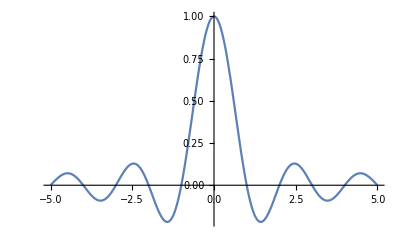

```mathematica
Plot[Sinc[d*Pi],{d,-5,5},PlotRange->Full]
```

Matlab uses a sinc function that crosses zero at x mod 1 = 1, dang.

```mathematica
Subscript[q5b$Ω, c]=Pi/4;
q5$hHighPass=((-Subscript[q5b$Ω, c]/Pi)*Sinc[(Subscript[q5b$Ω, c]*n/Pi)*(Pi/2)]/.n->q5$n)+(If[#==0,1,0]&/@q5$n);
```

```mathematica
q5b$y=ListConvolve[q5$hHighPass,x,1];

q5b$highPassed=ListPlay[q5b$y,SampleRate->fs]
```

-Graphics-

```mathematica
q5$handel
```

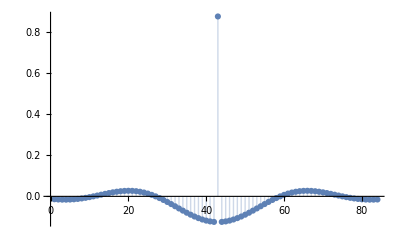

-Graphics-

```mathematica
ListPlot[q5$hHighPass,PlotRange->Full,Filling->Axis]
ListPlot[{
fftShift[q5$x]//Abs,
fftShift[q5b$y]//Abs
},PlotRange->All,Filling->Axis]
```

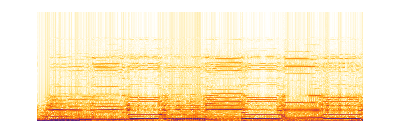

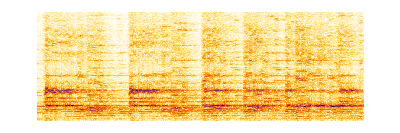

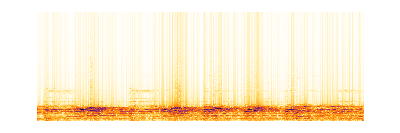

```mathematica
Spectrogram[q5b$highPassed]
Spectrogram[q5$handel]
Spectrogram[q5a$lowPassed]
```

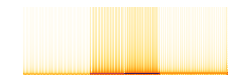

-Graphics-

-Graphics-

```mathematica
ts=TimeSeries[{{0,300},{1,400},{1.5,500},{2,600}}];
stuff=AudioGenerator[{"Sin",ts},3]
Spectrogram[stuff]

Subscript[stuff$Ω, c]=Pi/64;
stuff$n=Range[-42,41];
stuff$hHighPass=((-Subscript[stuff$Ω, c]/Pi)*Sinc[(Subscript[stuff$Ω, c]*n/Pi)*(Pi/2)]/.n->stuff$n)+(If[#==0,1,0]&/@q5$n);

stuff$y=ListConvolve[stuff$hHighPass,AudioData[stuff],1];

stuff$highPassed=ListPlay[stuff$y,SampleRate->QuantityMagnitude[AudioSampleRate[stuff]]]
Spectrogram[stuff$highPassed]
```

### 6.